# Pset02: molecular dynamics

## Part B: Triatomic reaction dynamics with Lennard-Jones potentials B1: The Lennard Jones Potential a)

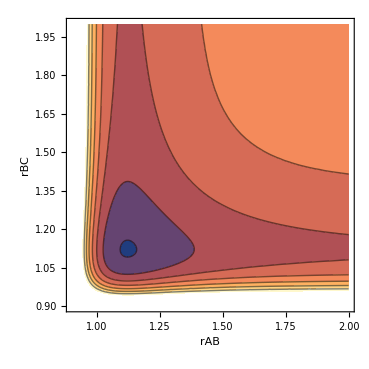

```mathematica
ClearAll["Global`*"]
Clear[Vlj, ϵ, rAB, rBC, σ, r];
ϵ=1.0;
σ=1.0;
Vlj[r_] = 4*ϵ*((σ/r)^12 - (σ/r)^6);
ContourPlot[Vlj[rAB] + Vlj[rBC] + Vlj[rAB+rBC], {rAB, 0.9, 2.0}, {rBC, 0.9, 2.0}, FrameLabel -> {"rAB","rBC"}]
```

```mathematica
solutions=Minimize[Vlj[rAB] + Vlj[rBC] + Vlj[rAB + rBC],{rAB,rBC}];
```

The configuration of the three atoms that gives a minimum potential energy of -2.03112 is the following:
	rAB = 1.12103 , rBC = 1.12103

## b)

```mathematica
mA = 1.0;mB = 1.0;mC = 1.0;
h = 0.02;
t = 4.0;
Ax=-3.0;Bx=0.0;Cx=1.3;
Av=1.0;Bv=0.0;Cv=0.0;
Flj[r_] = 24 ϵ(2(σ^12/r^13)-(σ^6/r^7));
x = {Ax, Bx, Cx};
v = {Av, Bv, Cv};
(*Verlet Algorithm*)
VerletAlgo[x0_, F0_, v0_, m_]:= Module[
	xk = x0;
	Fk = F0;
	vk = v0;
	
	xk1 = xk + h*vk + (Fk*h^2)/(2*m);
	Fk1 = Flj[xk1];
	vk1 = vk + ((h/2m)*(Fk + Fk1));
]
```

{-3.,0.,1.3}